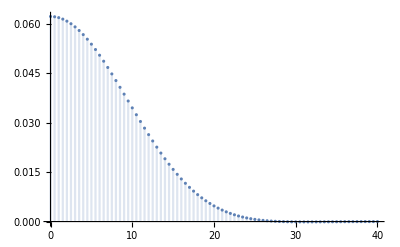

```mathematica
H[z_]:=1/8*RiemannXi[1/2+ⅈ*z/2]
DiscretePlot[{Re[H[z]], Im[H[z]]}, {z, 0, 40, 0.5}]
```

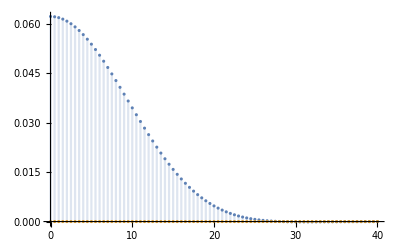

```mathematica
H[z_]:=-(1+z^2)*Pi^(-(1+ⅈ*z)/4)*Gamma[1/4+ⅈ*z/4]*Zeta[1/2+ⅈ*z/2]/64
DiscretePlot[{Re[H[z]], Im[H[z]]}, {z, 0, 40, 0.5}]
```

```mathematica
(*Zeta[2z]*)
RXi[z_]:=(-1)^(z+1)*z!/(2z)!*BernoulliB[2z]*2^(2z-1)*Pi^z*(2z-1)
Z2[z_]:=RXi[z]*Pi^z/(z(2z-1)*Gamma[z])
Z2s[z_] :=Simplify[Z2[z]]

StirlingFunction[n_]:=4*Sqrt[Pi*n/2]*(n/(2*Pi*E))^n
Simplify[ReplaceAll[Simplify[Function[z, Evaluate[Simplify[D[Z2s[z], {z, 2}]]]][10]], BernoulliB->StirlingFunction]]
```

(135179785203232049280 ⅇ^20 EulerGamma^2 π^20-56324910501346687200 ⅇ^20 π^22+2554783439592384000000000000000000000 ⅈ √10 π^(3/2) (-1+40 Log[2]-40 Log[20]+40 Log[π])+8710316077320 ⅈ ⅇ^20 π^21 (-55835135+15519504 Log[2]+15519504 Log[π])-263388153600000000000000000000 √(10 π) (-50637031+387987600 Log[2]^2-2772357370 Log[20]+387987600 Log[20]^2-10 Log[2] (-277235737+38798760 Log[4]+77597520 Log[20])+9699690 Log[4] (1+40 Log[20]-40 Log[π])+2791756750 Log[π]-387987600 Log[π]^2)+174611 ⅇ^20 π^20 (11256448518043769+774176799876480 Log[2]^2-2746577734562376 Log[4]-5570573149112400 Log[π]+774176799876480 Log[π]^2+77417679987648 Log[2] (-1+20 Log[π]))+99768240 EulerGamma √π (51214363200000000000000000000 √10 (-1+40 Log[2]-40 Log[20]+40 Log[π])+174611 ⅇ^20 π^(39/2) (-55835135+7759752 ⅈ π+7759752 Log[4]+15519504 Log[π])))/(296379936248814329236825500000 ⅇ^20)